## Section 2. Enter Tmat.

#### The matrix Tmat defined next is the TET example from Section 15.3 of TapeTape2021. It is also Eq (76) of TapeTape2022. Change Tmat to suit yourself, but of course Tmat must be symmetric. Tmat is the matrix [T]_𝔹𝔹 of your elastic map T with respect to the basis 𝔹.

```mathematica
Print[Now];
Tmat=1/64({{168, 4 √6, -40, 6 √6, 6 √2, 0}, {4 √6, 324, -4 √6, -42, -14 √3, 16 √3}, {-40, -4 √6, 168, -6 √6, -6 √2, 0}, {6 √6, -42, -6 √6, 233, 35 √3, -8 √3}, {6 √2, -14 √3, -6 √2, 35 √3, 163, -8}, {0, 16 √3, 0, -8 √3, -8, 352}});
denominator=64;
```

## Section 3. Output.

#### Choose one :

```mathematica
WantDetails="NoWantDetails"
```

```mathematica
WantDetails="WantDetails"
```

#### Σ = MONO

```mathematica
OutputFor[Tmat,MONO]
```

#### Σ = ORTH

```mathematica
OutputFor[Tmat,ORTH]
```

#### Σ = TET

```mathematica
OutputFor[Tmat,TET]
```

#### Σ = CUBE

```mathematica
OutputFor[Tmat,CUBE]
```

#### Σ = TRIG

```mathematica
OutputFor[Tmat,TRIG]
```

#### Σ = XISO

```mathematica
OutputFor[Tmat,XISO]
```

#### Σ = ISO

```mathematica
OutputFor[Tmat,ISO]
```

#### If β_Σ^T = 999 in the lattice, then you failed to evaluate OutputFor[Tmat, Σ] above.

```mathematica
LatticeOfDTs[Tmat]
Print["[T] = ",1/denominator,MatrixForm[denominator Tmat]]
```

#### From the lattice and the appropriate U you get the symmetry group of T. See Theorem 3of TapeTape2022.

```mathematica
FromTheorem3[Tmat]
```

#### As an example, ZRot[π/2] is in 𝕌_TET, so V = U ZRot[π/2] U^T should be a symmetry of T.

```mathematica
V=UT[Tmat,TET].ZRot[π/2].Transpose[UT[Tmat,TET]];
MatrixForm[Chop[V]]
MatrixForm[Chop[MatrixUbar[V].Tmat.Transpose[MatrixUbar[V]]-Tmat,10^-7]]
```

## Addendum: output from OutputFor

```mathematica
WantDetails="WantDetails"
```

#### Calling OutputFor assigns several variables

```mathematica
OutputFor[Tmat,MONO]
```

#### The triple of angles defining U for the closest to MONO

```mathematica
{θ0,σ0,ϕ0}
```

```mathematica
{θ0,σ0,ϕ0}/Degree
```

#### The U for the closest to MONO

```mathematica
MatrixForm[UT[Tmat,MONO]]
```

#### The distance to closest MONO

```mathematica
dT[Tmat,MONO]
```

#### The angular distance to closest MONO

```mathematica
βT[Tmat,MONO]/Degree
```

#### The closest to MONO map

```mathematica
MatrixForm[Closest[Tmat,MONO]]
```

#### Plot the 2D function that represents the search over U (specifically θ and ϕ)

```mathematica
ContourPlot[Alpha[Tmat,{θ,ϕ},MONO]/Degree,{θ,0,2π},{ϕ,0,π},ColorFunction->(ColorData["TemperatureMap"]),PlotLegends->Automatic,AspectRatio->Automatic,ImageSize->500]
```

#### Add the minimum as a green dot

```mathematica
Show[{ContourPlot[Alpha[Tmat,{θ,ϕ},MONO]/Degree,{θ,0,2π},{ϕ,0,π},ColorFunction->(ColorData["TemperatureMap"]),PlotLegends->Automatic],
Graphics[{PointSize[.015],{Green,Point[TPxyz0to2pi[UT[Tmat,MONO].{0,0,1}]]}}]},FrameTicks->{Range[0,2π,π],Range[0,π,π/2]},AspectRatio->Automatic,PlotRange->All,ImageSize->500]
```

## Examples of lattice maps for the matrices in Tape and Tape (2021)

#### TT21TRIV

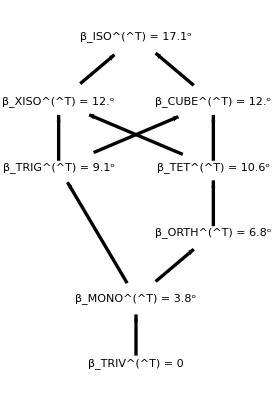

[T] = 1/5(5 | 0 | 0 | -2 | 0 | 0
0 | 6 | 0 | 0 | -2 | 0
0 | 0 | 5 | 0 | 0 | 0
-2 | 0 | 0 | 5 | 0 | 0
0 | -2 | 0 | 0 | 6 | 0
0 | 0 | 0 | 0 | 0 | 6)

#### TT21MONO

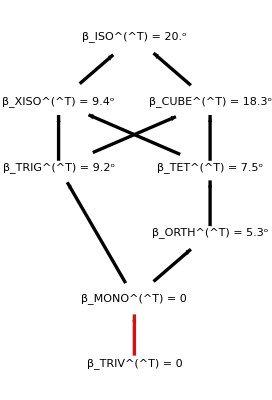

[T] = 1/80(222 | -12 √6 | -82 | 21 √6 | -39 √2 | 0
-12 √6 | 196 | 12 √6 | 30 | 10 √3 | -16
-82 | 12 √6 | 222 | 9 √6 | -51 √2 | 0
21 √6 | 30 | 9 √6 | 242 | -6 √3 | -24
-39 √2 | 10 √3 | -51 √2 | -6 √3 | 254 | -8 √3
0 | -16 | 0 | -24 | -8 √3 | 304)

#### TT21ORTH

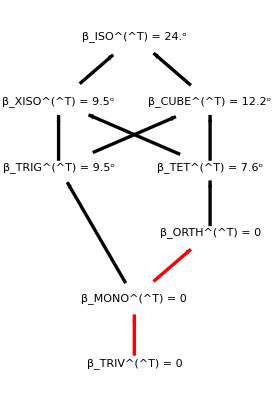

[T] = 1/10(38 | 18 | 3 √2 | -5 √2 | -√6 | -2 √2
18 | 38 | 3 √2 | 5 √2 | -√6 | -2 √2
3 √2 | 3 √2 | 41 | 0 | -7 √3 | 6
-5 √2 | 5 √2 | 0 | 20 | 0 | 0
-√6 | -√6 | -7 √3 | 0 | 27 | -2 √3
-2 √2 | -2 √2 | 6 | 0 | -2 √3 | 56)

#### TT21TET

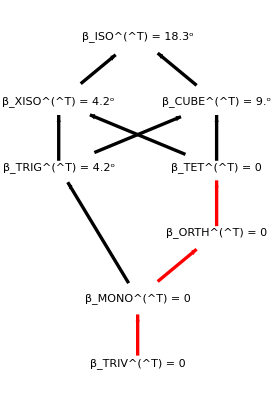

[T] = 1/64(168 | 4 √6 | -40 | 6 √6 | 6 √2 | 0
4 √6 | 324 | -4 √6 | -42 | -14 √3 | 16 √3
-40 | -4 √6 | 168 | -6 √6 | -6 √2 | 0
6 √6 | -42 | -6 √6 | 233 | 35 √3 | -8 √3
6 √2 | -14 √3 | -6 √2 | 35 √3 | 163 | -8
0 | 16 √3 | 0 | -8 √3 | -8 | 352)

#### TT21XISO

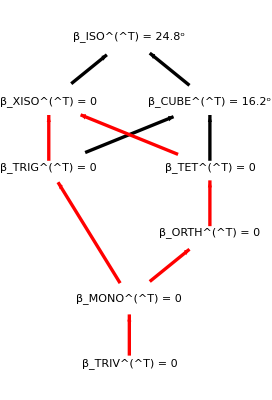

[T] = 1/128(532 | 92 √3 | 122 | -2 √3 | -60 | 48
92 √3 | 348 | -2 √3 | 126 | -20 √3 | 16 √3
122 | -2 √3 | 349 | 31 √3 | -126 | 24
-2 √3 | 126 | 31 √3 | 287 | -42 √3 | 8 √3
-60 | -20 √3 | -126 | -42 √3 | 212 | -16
48 | 16 √3 | 24 | 8 √3 | -16 | 704)

#### TT21CUBE

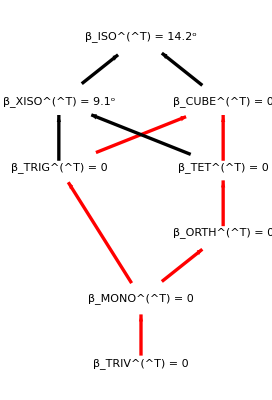

[T] = 1/36(52 | 4 | 16 | -6 | -2 √3 | 0
4 | 64 | 4 | 12 | 4 √3 | 0
16 | 4 | 52 | -6 | -2 √3 | 0
-6 | 12 | -6 | 45 | 3 √3 | 0
-2 √3 | 4 √3 | -2 √3 | 3 √3 | 39 | 0
0 | 0 | 0 | 0 | 0 | 108)

#### TT21TRIG

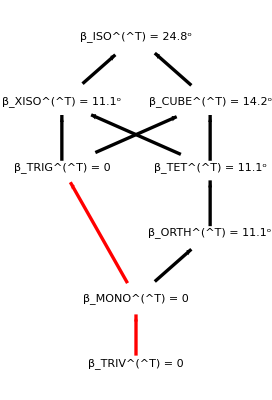

[T] = 1/16(4 (8-√3) | -8 | 3 √2 | -6 √2 | -3 √6 | 0
-8 | 4 (8+√3) | 3 √2 | 6 √2 | -3 √6 | 0
3 √2 | 3 √2 | 76 | -2 √3 | 12 √3 | 4 √3
-6 √2 | 6 √2 | -2 √3 | 24 | 6 | 0
-3 √6 | -3 √6 | 12 √3 | 6 | 52 | 4
0 | 0 | 4 √3 | 0 | 4 | 88)

#### TT21ISO

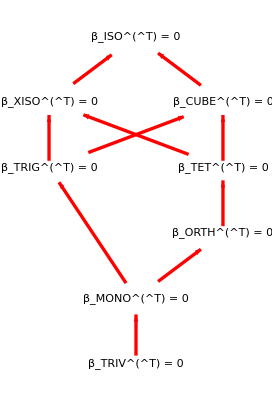

[T] = 1(3 | 0 | 0 | 0 | 0 | 0
0 | 3 | 0 | 0 | 0 | 0
0 | 0 | 3 | 0 | 0 | 0
0 | 0 | 0 | 3 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0
0 | 0 | 0 | 0 | 0 | 1)